## Initialize

It may be easiest to set the notebook directory to the file where the images are stored, in order to import using shorter file names:

```mathematica
SetDirectory["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Temp 4D STEM data/35 May 2021 TEAM 0.5"]
```

/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Temp 4D STEM data/35 May 2021 TEAM 0.5

## Moire spacings in HR-STEM images and their FFTs:

```mathematica
auNP1=Import["Au NP on MoS2 champion3 12pm ppx.tif"]
```

-Graphics-

```mathematica
ImageCrop[ImageAdjust[ImagePeriodogram[auNP1],{0,0.2,1.8}],512]
```

-Graphics-

```mathematica
mos2film=Import["thin film atoms 16p9pm ppx_2.tif"]
```

-Graphics-

```mathematica
mos2film=ImageTake[Import["thin film atoms 16p9pm ppx_2.tif"],{200,800},{400,1000}]
```

-Graphics-

```mathematica
ImageCrop[ImageAdjust[ImagePeriodogram[mos2film],{0,0.2,1.8}],512]
```

-Graphics-

```mathematica
auNP2=Import["au111 on mos2 champion image 16p9pm ppx_2.tif"]
```

-Graphics-

```mathematica
fftall=ImageCrop[ImageAdjust[ImagePeriodogram[auNP1],{0,0.2,1.8}],512]
```

-Graphics-

```mathematica
mos2=ImageTake[auNP2,{200,380},{520,700}]
```

-Graphics-

```mathematica
ImageTake[auNP2,{400,580},{520,700}]
```

-Graphics-

```mathematica
fft2=ImagePeriodogram[ImageTake[auNP2,{400,580},{520,700}]]
```

-Graphics-

```mathematica
fftmos2=ImagePeriodogram[mos2]
```

-Graphics-

Au

```mathematica
Import["twisted bilayer and Au NPs 16p9pm ppx.tif"]
```

-Graphics-

```mathematica
twist=ImageTake[Import["twisted bilayer and Au NPs 16p9pm ppx.tif"],{100,750},{0,650}]
```

-Graphics-

```mathematica
fftTwist=ImageCrop[ImageAdjust[ImagePeriodogram[twist],{0,0.2,1.8}],325]
```

-Graphics-

```mathematica
twistNP=Import["au NPs on layered mos2 16p9pm ppx.tif"]
```

-Graphics-

```mathematica
fftNPTwist=ImageCrop[ImageAdjust[ImagePeriodogram[twistNP],{0,0.2,1.8}],512]
```

-Graphics-

```mathematica
moire=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Temp 4D STEM data/march2020_team05_moire_108pm_ppx.tif"]
```

-Graphics-

```mathematica
moire=ImageTake[Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Temp 4D STEM data/march2020_team05_moire_108pm_ppx.tif"], {300,900},{300,900}]
```

-Graphics-

```mathematica
fftMoire=ImageCrop[ImageAdjust[ImagePeriodogram[moire],{0,0.2,1.8}],300]
```

-Graphics-

```mathematica
moire2=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Temp 4D STEM data/march2020_team05_moire_13p4pm_ppx.tif"]
```

-Graphics-

```mathematica
moire2=ImageTake[Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Temp 4D STEM data/march2020_team05_moire_13p4pm_ppx.tif"],{300,1000},{100,800}]
```

-Graphics-

```mathematica
fftMoire=ImageCrop[ImageAdjust[ImagePeriodogram[moire2],{0,0.2,1.8}],300]
```

-Graphics-

```mathematica
moireApril2021=Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Temp 4D STEM data/34 April 2021/sample_D8_0018_161_pm_ppx.tif"]
```

-Graphics-

```mathematica
fftMoireApril2021=ImageCrop[ImageAdjust[ImagePeriodogram[moireApril2021],{0,0.2,1.8}],512]
```

-Graphics-

```mathematica
moireJune2019=ImageTake[Import["/Users/clarissa/Google Drive/Joel Ager Group/4D STEM project/Temp 4D STEM data/15 June 19/June 19 HAADF zoom moire 452pm_ppx.tif"],
{1,900},{1,900}]
```

-Graphics-

```mathematica
fftMoireJune2019=ImageCrop[ImageAdjust[ImagePeriodogram[moireJune2019],{0,0.2,1.8}],900]
```

-Graphics-

## Moire spacings in HR-STEM images measured over 4-5 fringes (in nm):

```mathematica
spacings=N@{8.68/5,8.38/5,8.11/5,7.93/5,8.44/5,7.70/4,5.58/3,8.33/5,8.52/5,7.04/4,7.18/4,7.19/4,7.2/4,8.78/5,8.35/5,92/5,130/8}
```

{1.736,1.676,1.622,1.586,1.688,1.925,1.86,1.666,1.704,1.76,1.795,1.7975,1.8,1.756,1.67,18.4,16.25}

Moire magnification factor for a particular image where the Moire spacing was 15.8 nm

```mathematica
magFactor=15.8/1.58
```

10.

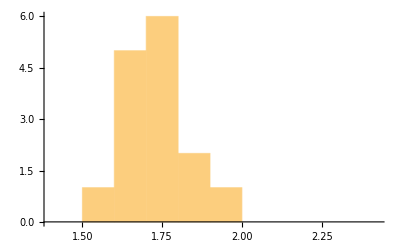

```mathematica
Histogram[spacings,{0.1}]
```

## Making a model to experiment with Moire patterns:

From https://mathematica.stackexchange.com/questions/61834/how-to-create-an-hexagonal-lattice-structure:

```mathematica
unitCell[x_,y_]:={RGBColor[1.,0.58,0.83],Disk[{x,y},0.1],RGBColor[0.21,0.63,1.],Disk[{x,y+2/3 Sin[120 Degree]},0.2],Gray,
,Line[{{x,y},{x,y+2/3 Sin[120 Degree]}}],Line[{{x,y},{x+Cos[30 Degree]/2,y-Sin[30 Degree]/2}}],Line[{{x,y},{x-Cos[30 Degree]/2,y-Sin[30 Degree]/2}}]}
```

```mathematica
Graphics[unitCell[0,0],ImageSize->100]
```

-Graphics-

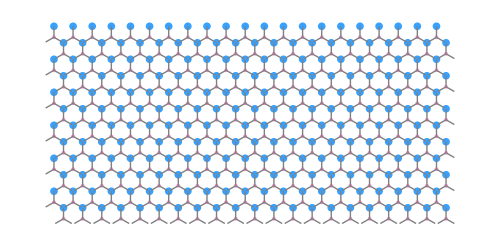

```mathematica
l1=Graphics[Block[{unitVectA={Cos[120 Degree],Sin[120 Degree]},unitVectB={1,0}},Table[unitCell@@(unitVectA j+unitVectB k),{j,1,12},{k,Ceiling[j/2],20+Ceiling[j/2]}]],ImageSize->500]
```

```mathematica
unitCell2[x_,y_]:={White,Disk[{x,y},0.1],RGBColor[0.21,0.63,1.],Disk[{x,y+2/3 Sin[120 Degree]},0.2]}
```

```mathematica
Graphics[unitCell2[0,0],ImageSize->100]
```

-Graphics-

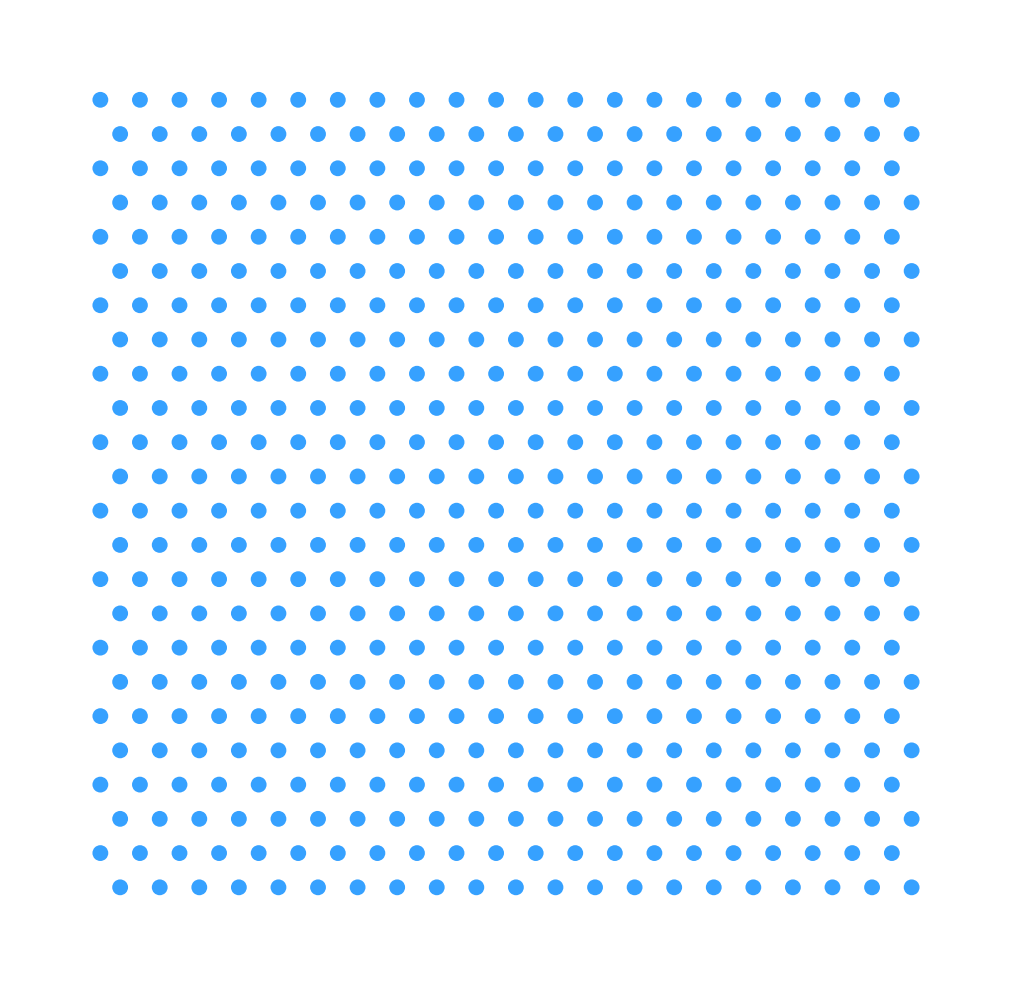

```mathematica
l2=Graphics[Block[{unitVectA={Cos[120 Degree],Sin[120 Degree]},unitVectB={1,0}},Table[unitCell2@@(unitVectA j+unitVectB k),{j,1,24},{k,Ceiling[j/2],20+Ceiling[j/2]}]],ImageSize->500]
```